## Prepare

```mathematica
imgSize=600;
```

```mathematica
SetDirectory[ToString[ParentDirectory@ParentDirectory@NotebookDirectory[]]<>"/equilibrium/images"]
```

/Users/leima/GitHub/StatisticalPhysics/equilibrium/images

## Specific Heat

Specific heat of QHO

```mathematica
ene=-D[Log[1/ (2Sinh[beta hbar omega/2])],beta]//FullSimplify
```

1/2 hbar omega Coth[(beta hbar omega)/2]

```mathematica
sheat=D[ene,beta]D[1/(kB T),T]//FullSimplify
```

(hbar^2 omega^2 Csch[(beta hbar omega)/2]^2)/(4 kB T^2)

```mathematica
Limit[sheat,beta->0]
```

(hbar^2 omega^2 DirectedInfinity[1/(Sign[hbar]^2 Sign[omega]^2)])/(kB T^2)

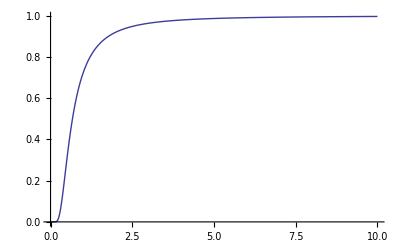

```mathematica
Plot[1/T^2 (Csch[1/T])^2,{T,0,10},AxesOrigin->{0,0}]
```

## Grid Lines

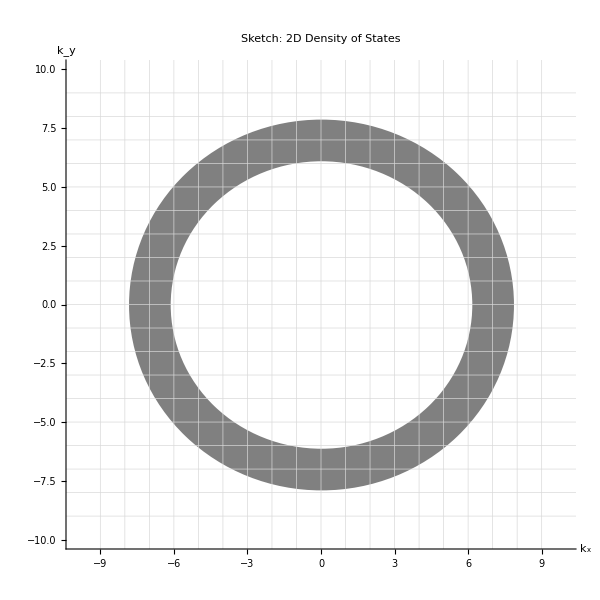

2DDoS.png

```mathematica
Graphics[{Thickness[0.05],Gray,Circle[{0,0},7]},GridLines->{Table[j,{j,-9,9}],Table[i,{i,-9,9}]},Axes->True,AxesLabel->{Style["k_x",Large],Style["k_y",Large]},PlotRange->{{-10,10},{-10,10}},PlotLabel->Style["Sketch: 2D Density of States",Large],ImageSize->imgSize]
Export["2DDoS.png",%]
```